```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
A={1/2 {1,0,1},{0,0,1},{0,1/2,1/2}};
```

```mathematica
B= Inverse[Transpose[A] ]
```

{{2,0,0},{-1,-1,1},{0,2,0}}

```mathematica
b=Sort[Transpose[Tally[Flatten[Table[Table[Table[Norm[h B[[1]]+k B[[2]]+l B[[3]]],{h,-5,5}],{k,-5,5}],{l,-5,5}],3]]][[1]],#1<#2&][[2;;5]]
```

{√3,2,2 √2,√11}

```mathematica
T=2 ArcSin[x/2*b]/Pi*180;
```

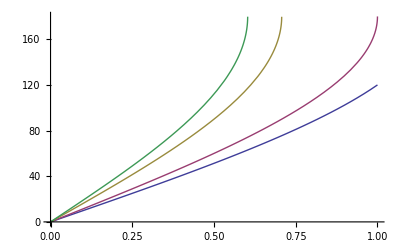

```mathematica
Plot[{T},{x,0,1}]
```

```mathematica
Solve[T[[1]]==42.2,x]
T/.%
```

{{x→0.415689}}

{{42.2,49.1254,72.0123,87.156}}

```mathematica
1.5/0.4156885081510353
```

3.60847